```mathematica
Module[{bn,phase,xsol,tie,y1,y2,x1,x2,plot1},
bn=Sequence[PlotStyle->{Thick,Black}];

phase[x_]:=-1.551*x^2+1.536*x;

xsol[y0_,n_]:=Quiet[x/.Solve[phase[x]==y0,x][[n]]];

tie[xA_,yA_,xB_,yB_,x_]:=((yB-yA)/(xB-xA))*(x-xA)+yA;

y1:={0.08,0.12,0.18,0.21,0.28}*√3/2;
y2:={0.02,0.1,0.25,0.38,0.43}*√3/2;

x1:=Table[xsol[y1[[n]],1],{n,1,5}];
x2:=Table[xsol[y2[[n]],2],{n,1,5}];

plot1=Show[
Graphics[{
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
Table[{Text[Style[1-j,15],{1.04-j/2,j*√3/2}],Rotate[Text[Style[j,15],{j/2-0.025,j*√3/2+0.025}],-55 Degree],Rotate[Text[Style[1-j,15],{j-0.015,-0.035}],55 Degree]},{j,0.1,0.9,0.1}],
{PointSize[0.02],Red,Table[{Point[{x1[[n]],y1[[n]]}],Point[{x2[[n]],y2[[n]]}]},{n,1,5}]}
}],
Plot[phase[x],{x,0.,0.99},Evaluate@bn],
(*Table[Plot[tie[x1[[n]],y1[[n]],x2[[n]],y2[[n]],x],{x,x1[[n]],x2[[n]]},PlotStyle->{Thick,Black}],{n,1,5}],*)

(*Plot[tie[xsol[0.08*√3/2,1],0.08*√3/2,xsol[0.02*√3/2,2],0.02*√3/2,x],{x,xsol[0.08*√3/2,1],xsol[0.02*√3/2,2]},Evaluate@bn],
Plot[tie[xsol[0.12*√3/2,1],0.12*√3/2,xsol[0.1*√3/2,2],0.1*√3/2,x],{x,xsol[0.12*√3/2,1],xsol[0.1*√3/2,2]},Evaluate@bn],
Plot[tie[xsol[0.18*√3/2,1],0.18*√3/2,xsol[0.25*√3/2,2],0.25*√3/2,x],{x,xsol[0.18*√3/2,1],xsol[0.25*√3/2,2]},Evaluate@bn],
Plot[tie[xsol[0.21*√3/2,1],0.21*√3/2,xsol[0.38*√3/2,2],0.38*√3/2,x],{x,xsol[0.21*√3/2,1],xsol[0.38*√3/2,2]},Evaluate@bn],
Plot[tie[xsol[0.28*√3/2,1],0.28*√3/2,xsol[0.43*√3/2,2],0.43*√3/2,x],{x,xsol[0.28*√3/2,1],xsol[0.43*√3/2,2]},Evaluate@bn],*)
ImageSize->{600,400}];

(*Plot[Simplify@tie[xsol[0.08*√3/2,1],0.08*√3/2,xsol[0.02*√3/2,2],0.02*√3/2,x],{x,0,1}]*)
(*Plot[-0.05578*x+0.07192,{x,0,1}]*)
(*Table[Simplify@tie[x1[[n]],y1[[n]],x2[[n]],y2[[n]],x],{n,1,5}]*)
(*Show[Table[Plot[Simplify@tie[x1[[n]],y1[[n]],x2[[n]],y2[[n]],x],{x,0,1}],{n,1,5}]]*)

(*Show[
Plot[phase[x],{x,0.,0.99},Evaluate@bn],
Table[
Plot[{-0.05578*x+0.07192,-0.0202*x+0.1054,0.08595*x+0.146,0.273*x+0.1443,0.3516*x+0.1732}[[i]],{x,x1[[i]],x2[[i]]}],
{i,1,5}],
PlotRange->{0,√3/2}]*)

Column[{x1,x2}]
]
```

{0.0473715,0.0730461,0.114794,0.13749,0.197095}
{0.978921,0.930309,0.82012,0.676848,0.566512}

```mathematica
{-0.05578*x+0.07192,-0.0202*x+0.1054,0.08595*x+0.146,0.273*x+0.1443,0.3516*x+0.1732}
```

```mathematica
Module[{yPhase,x1,x2,y,y1,y2},
yPhase[x_]:=-1.551*x^2+1.536*x;

x1:={0.04737,0.07305,0.1148,0.15(*0.1375*),0.1971};
x2:={0.9789,0.9303,0.8201,0.6768,0.5665};

(*y[x_]:={-0.05578*x+0.07192,-0.0202*x+0.1054,0.08595*x+0.146,0.273*x+0.1443,0.3516*x+0.1732};*)
y1:=yPhase[x1];
y2:=yPhase[x2];
(*y[x_]:=(0.0093*n^2+0.0131*n)*x+(-0.0017*n^2+0.0352*n);
x1:=x/.Solve[y[x]==yPhase[x],x][[1]];
x2:=x/.Solve[y[x]==yPhase[x],x][[2]];
y1:=yPhase[x1];
y2:=yPhase[x2];*)

(*Show[
Plot[yPhase[x],{x,0,0.99},PlotStyle->{Thick,Black}],
Graphics[{
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
(*{PointSize[0.025],Red,Table[{Point[{x1[[n]],y1[[n]]}],Point[{x2[[n]],y2[[n]]}]},{n,1,5}]},
{Thick,Blue,Table[Line[{{x1[[n]],y1[[n]]},{x2[[n]],y2[[n]]}}],{n,1,5}]}*)
{Thick,Table[Line[{{x1,y1},{x2,y2}}],{n,1,5}]}
}],
PlotRange->{0,√3/2},AspectRatio->1,Axes->False]*)
Table[Simplify[((y2[[n]]-y1[[n]])/(x2[[n]]-x1[[n]]))*(x-x1[[n]])+y1[[n]]],{n,1,5}]
]
```

{0.0719206-0.0557448 x,0.105404-0.0201958 x,0.146023+0.0859701 x,0.157458+0.253633 x,0.17318+0.351656 x}

```mathematica
tie[x_]:={-0.05574*x+0.07192,-0.0202*x+0.1054,0.08597*x+0.146,0.2536*x+0.1575,0.3517*x+0.1732}
```

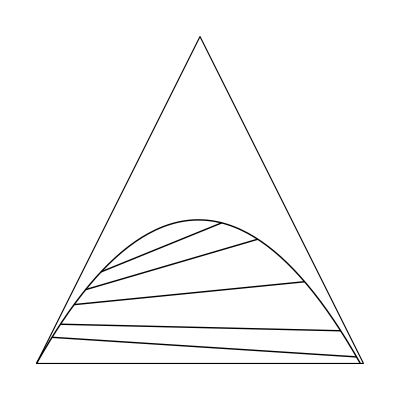

```mathematica
Module[{yPhase,tie,x1,x2},
yPhase[x_]:=-1.551*x^2+1.536*x;

tie[x_,n_]:={-0.05574*x+0.07192,-0.0202*x+0.1054,0.08597*x+0.146,0.2536*x+0.1575,0.3517*x+0.1732}[[n]];

x1:=x/.Solve[tie[x,n]==yPhase[x],x][[1]];
x2:=x/.Solve[tie[x,n]==yPhase[x],x][[2]];

Show[
Plot[yPhase[x],{x,0,0.99},PlotStyle->{Thick,Black}],
Graphics[{
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
{Thick,Table[Line[{{x1,yPhase[x1]},{x2,yPhase[x2]}}],{n,1,5}]}
}],
PlotRange->{0,√3/2},AspectRatio->1,Axes->False]
]
```